Projecting Data

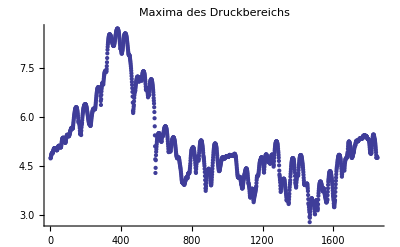

Clustering Training-portion

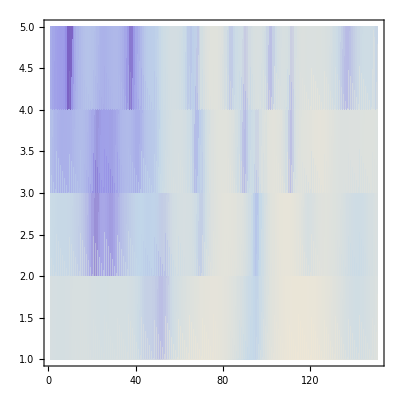

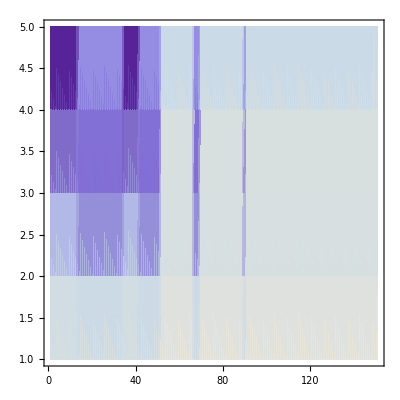

max windows now...

Durchschnitt des Ruhedrucks: 1.10258

Making Plots

-Graphics-

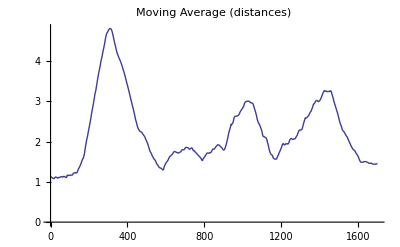

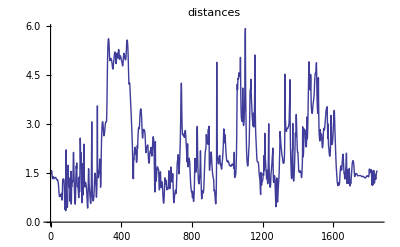

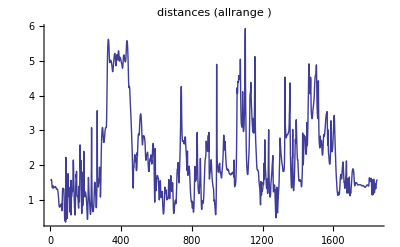

```mathematica
ClearAll[ComputeCentroids,data,data3,data2,cl2,numClusters,startIdx,endIdx,MinDist,centers,meanTrainingSet,startTraining,endTraining,schluckEndeStartPos,ruhedruck,ReadMarkers,markers,schluck];
schluck="7";
directory="M:\\Proband1\\00506534Schluck"<>schluck<>".ASC.data";
dataDruck=(Import[directory<>"\\data.csv","Data","HeaderLines"->0]);
data=(Import[directory<>"\\result.csv","Data","HeaderLines"->0]);


data=data[[All,1;;(Length[data[[1,All]]]+1)/2]];

numClusters=3;
startIdx=ToExpression[StringTake[(Import[directory<>"\\channelstart","Data","HeaderLines"->0]),{2}][[1]]]+1;
endIdx=ToExpression[StringTake[(Import[directory<>"\\channelend","Data","HeaderLines"->0]),{2}][[1]]]+1;

ReadMarkers[base_]:=(

start1=Import[base<>"\\rdstart","Data","HeaderLines"->0][[1]];
ende1=Import[base<>"\\rdend","Data","HeaderLines"->0][[1]];
samplerate1=Import[base<>"\\samplerate","Data","HeaderLines"->0][[1]];
start2=StringSplit[start1,":"];
start3=ToExpression[start2[[2]]]+ToExpression[start2[[1]]]*60;
ende2=StringSplit[ende1,":"];
ende3=ToExpression[ende2[[2]]]+ToExpression[ende2[[1]]]*60;
Return[{start3*ToExpression[samplerate1],ende3*ToExpression[samplerate1]}];

);

markers=ReadMarkers[directory];
startTraining=markers[[1]]-data[[1,1]];
endTraining=markers[[2]]-data[[1,1]];


ComputeCentroids[clusteringComponents_,data_,numClusters_]:=(
centers=Reap[
For[i=1,i≤numClusters,i++,(
Clear[centroid,cnt];
centroid=Table[0,{i,endIdx-startIdx+1}];

cnt=0;
For[j=1,j≤Length[data],j++,(
If[clusteringComponents[[j]]==i,(
centroid+=data[[j]];
cnt++;
)];
)]; (*of For - data*)
centroid/=cnt;
Sow[centroid,sowcentroid]
(*Print["Centroid for cluster ",i,  " is ", centroid];
Print["Sample distance: ", ToString[EuclideanDistance[data[[1]],centroid]//N]];*)

)];

,sowcentroid];
Return[Flatten[centers[[2]],1]];
);

MinDist[list_,data_]:=(
ret=100000000000000;
For[j=1,j≤Length[list],j++,(
Clear[dist];
dist=EuclideanDistance[list[[j]],data];
ret=Min[ret,dist];
)];
(*Print[ret];*)
Return[ret];
);


FindIndex[distancesList_,startSeekIndex_,valueToFind_]:=(
l=Length[distancesList];
(*Print[distancesList]*);
idx=startSeekIndex;
(*Print["Start seeking for value ",ToString[valueToFind]," from Index ",ToString[startSeekIndex]];*)
While[idx≤l,(
If[distancesList[[idx]]≤valueToFind,Return[idx]];
idx++;
)];
Return[Length[distancesList]];
);
MaxIdx[list_]:=(
m=Max[list];
For[j=1,j≤Length[list],j++,(
If[list[[j]]==m,(
Return[j]
)];
)];
);
MinIdx[list_,idx_]:=(
t=idx;
c=list[[t]];
p=list[[t+1]];
d=+1;
If[p<c,d=1,d=-1];
While[list[[t+d]]<list[[t]],t=t+d];
Return[t];

);

Print["Projecting Data"];
data2=data[[startTraining;;endTraining,startIdx;;endIdx]];
data3=data[[All,startIdx;;endIdx]];
data4=data[[All,2;;20]];
(*
Berechnet das jeweilige Max des Sensor-bereichs über die gesamten Daten.
Ziel ist die Identifizierung des Max-Drucks in dem gesamten Bereich, von dem aus 
die Suche des Ruhedrucks starten wird.
*)

maxWindow=ParallelTable[Max[data[[i,startIdx;;endIdx]]],{i,1,Length[data[[All,1]]]}];
(*normWindow=ParallelTable[Norm[data[[i,2;;48]]],{i,0,Length[data[[All,1]]]}];*)
ListPlot[maxWindow,PlotRange->All, PlotLabel->"Maxima des Druckbereichs"] 
(*ListPlot[normWindow,PlotRange->All, PlotLabel->"Norm gesamt"] *)
schluckEndeStartPos=MaxIdx[maxWindow];

(*
Clustern des Trainings-Bereichs. Der Ruhedruck wird später ermittelt, indem die Messdaten einem der Cluster am nächsten kommt.
*)
Print["Clustering Training-portion"];
cl2=ClusteringComponents[data2,numClusters,1,DistanceFunction->EuclideanDistance,Method->"KMeans"];
centers=ComputeCentroids[cl2,data2,numClusters];
centroidList=Table[centers[[cl2[[i]]]],{i,1,Length[cl2]}];
ListDensityPlot[data[[startTraining;;endTraining,startIdx;;endIdx]]//Transpose]
ListDensityPlot[centroidList//Transpose]
(*,PlotStyle->{{Thick,Red},{Thick,Green}} *)

Print["max windows now..."]
(* Die jeweilige Distanz der Messung zu den clustern (hier die minimale Distanz zu den trainings-clustern) *)
distances=Map[MinDist[centers,#]&,data3];
(*Determine mean from training set*)
meanTrainingSet=Mean[distances[[startTraining;;endTraining]]];
Print["Durchschnitt des Ruhedrucks: ",meanTrainingSet//N];
startSearch=MaxIdx[maxWindow];
(*Methode 1*)
ruhedruck=FindIndex[distances,startSearch,meanTrainingSet];
(* Methode 2 *)
smooth=MovingAverage[distances,149];
startSearch=MaxIdx[smooth]+5;
ruhedruck=MinIdx[smooth,startSearch];

Print["Making Plots"];
daten=ListContourPlot[dataDruck[[All,2;;20]]//Transpose,PlotRange->All,Contours->10];
marker=Graphics[{Red,Rectangle[{ruhedruck-3,1},{ruhedruck+3,endIdx-startIdx+1}]}];
markerTrainLeft=Graphics[{Green,Rectangle[{startTraining-3,1},{startTraining+3,endIdx-startIdx+1}]}];
markerTrainRight=Graphics[{Green,Rectangle[{endTraining-3,1},{endTraining+3,endIdx-startIdx+1}]}];
bild1=Show[{daten,marker,markerTrainLeft,markerTrainRight}]
(* ListPlot[Flatten[cl2,0]]*)
(* ListContourPlot[centroidList//Transpose]*)
(*Export["c:/work/"<>schluck<>".png",bild1]*)

(*ListDensityPlot[data//Transpose,ColorFunction->Hue]*)

ListPlot[MovingAverage[distances,149],Joined->True, PlotLabel->"Moving Average (distances)"]
ListPlot[distances,Joined->True,PlotLabel->"distances"]

ListPlot[distances,Joined->True,PlotRange->All, PlotLabel->"distances (allrange )"]
```